```mathematica
(*Task One:*)

U=3*N*kB*T;  (*Based on the Equipartition Theorem*)
Cv=D[U,T]    (*Dulong-Petit Law*)
```

3 kB N

```mathematica
(*鉴于N是Wolfram的内部函数，故修改变量名称为 NA=6.022*10^23；即 Avogadro's constant；
由此规定了1mol物质的量。*)

U=3*NA*kB*T;  (*Based on the Equipartition Theorem*)
Cv=D[U,T]     (*Dulong-Petit Law*)
```

3 kB NA

```mathematica
(*Task Two:*)

U=3 N A(hb w/2)+(3 NA hb w)/(Exp[hb w/(kB T)]-1);  
(*Based on the Energy Quantum Hypothesis.*)
Cv=D[U,T]                                          
(*Einstein Model of Solid-State Heat Capacity*)
```

(3 ⅇ^((hb w)/(kB T)) hb^2 NA w^2)/((-1+ⅇ^((hb w)/(kB T)))^2 kB T^2)

```mathematica
(*Task Three:*)

(*w:Vibration frequency of a harmonic oscillator;QE:Einstein characteristic temperature;*)

Cv/.{w->kB QE/hb}   (*Transformation rules*)
```

(3 ⅇ^(QE/T) kB NA QE^2)/((-1+ⅇ^(QE/T))^2 T^2)

(4.34399×10^7 ⅇ^(1320/T))/((-1+ⅇ^(1320/T))^2 T^2)

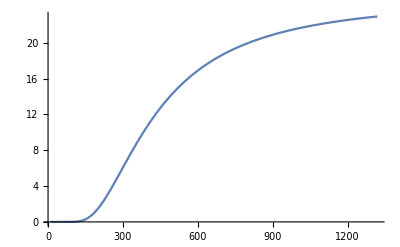

```mathematica
(*Task Four:*)
Cv=3 NA kB*(QE/T)^2*(Exp[QE/T]/(Exp[QE/T]-1)^2)
NA=6.022*10^23;  (*Avogadro's constant*)
kB=1.38*10^-23;  (*Boltzmann constant*)
QE=1320;  (*Einstein characteristic temperature*)
Plot[Cv,{T,10,1320}]
```